```mathematica
Module[{pk,lista},
pk[z_]:=z+0.25*Sin[π*z^0.8]^0.9;
lista=Table[{m,pk[m]},{m,0,1,0.01}];
FindFormula[lista,f]
]
```

0.0199806+2.23638 #1-2.05782 #1^2.+0.807228 #1^2.7351&

```mathematica
y[f_]:=2.24f-2.06 f^2+0.82 f^2.7;
```

```mathematica
y[0]
```

0.

```mathematica
y[1]
```

1.

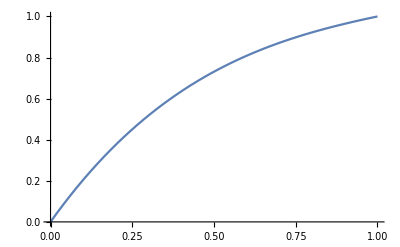

```mathematica
Plot[y[x],{x,0,1}]
```

```mathematica
Module[{pk,lista},
pk[z_]:=z^0.75+0.12*Sin[2π*z];
lista=Table[{m,pk[m]},{m,0,1,0.01}];
FindFormula[lista,f]
]
```

0.0156043+2.55513 f-1.94145 f^2-6.25648 f^3+11.5427 f^4-4.91471 f^5

```mathematica
q[f_]:=2.56f-1.94 f^2-6.26 f^3+11.54 f^4-4.9 f^5;
```

```mathematica
q[1]
```

1.

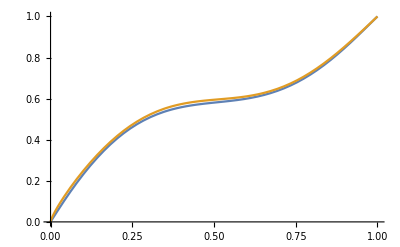

```mathematica
Plot[{q[x],x^0.75+0.12*Sin[2π*x]},{x,0,1}]
```

```mathematica
Solve[q[f]==f,f]
```

{{f→-0.44291},{f→0.},{f→0.6},{f→1.},{f→1.19801}}

```mathematica
q[0.6]
```

0.6

```mathematica
Module[{pk,lista},
pk[z_]:=z^0.9-0.14*Sin[2π*z];
lista=Table[{m,pk[m]},{m,0,1,0.01}];
FindFormula[lista,f]
]
```

0.00168674+0.512782 f-1.95367 f^2+11.3347 f^3-7.40401 f^4-13.0603 f^5+16.641 f^6-5.07199 f^7

```mathematica
k[f_]:=0.5f-2 f^2+11.4 f^3-7.4 f^4-13 f^5+16.5 f^6-5 f^7;
```

```mathematica
k[0]
```

0.

```mathematica
k[1]
```

1.

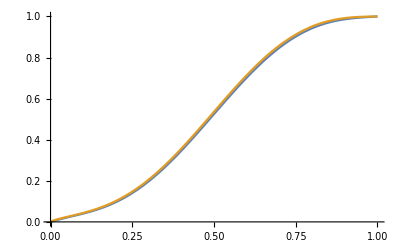

```mathematica
Plot[{k[x],x^0.9-0.14*Sin[2π*x]},{x,0,1}]
```

```mathematica
Solve[k[f]==f,f]
```

{{f→-0.803924},{f→-0.136705},{f→0.},{f→0.469923},{f→1.},{f→1.38535-0.130791 ⅈ},{f→1.38535+0.130791 ⅈ}}